# MixedEulerianGraphQ

Yields True if the strongly connected mixed graph g is Eulerian or unicursal, and False otherwise

## Definition

```mathematica
ClearAll[MixedEulerianGraphQ]
MixedEulerianGraphQ[graph_?(ConnectedGraphQ[#]∧MixedGraphQ[#]&)]:=AllTrue[Subsets[VertexList[graph]],EdgeCount[graph,Alternatives@@#->_](*arcs leaving*)-EdgeCount[graph,_->Alternatives@@#](*arcs entering*)<=EdgeCount[graph,_<->Alternatives@@#]&](*incident edges*)(*balanced set condition*)∧AllTrue[VertexDegree[graph],EvenQ](*even condition*)
```

## Documentation

### Usage

MixedEulerianGraphQ[g]

Yields Truepaclet:ref/True if the strongly connected mixed graph g is Eulerian or unicursal, and Falsepaclet:ref/False otherwise.

### Details & Options

Eulerian graphs have applications in arc routing and operations research.

EulerianGraphQ works for undirected graphs, directed graphs, and multigraphs but not mixed graphs. This function meets that need.

## Examples

### Basic Examples

Test if a mixed graph is Eulerian:

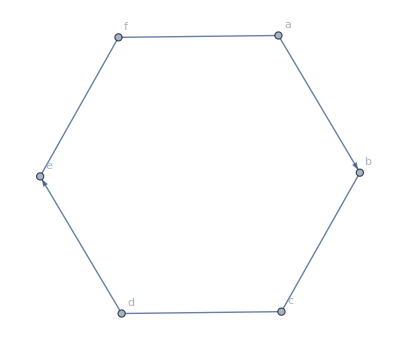

```mathematica
Graph[{a,b,c,d,e,f},{a->b,b<->c,c<->d,d->e,e<->f,a<->f},VertexLabels->Automatic,ImageSize->Automatic]
```

```mathematica
MixedEulerianGraphQ[Graph[{a,b,c,d,e,f},{a->b,b<->c,c<->d,d->e,e<->f,a<->f},VertexLabels->Automatic,ImageSize->Automatic]]
```

True

Test an even graph that violates the balanced set condition:

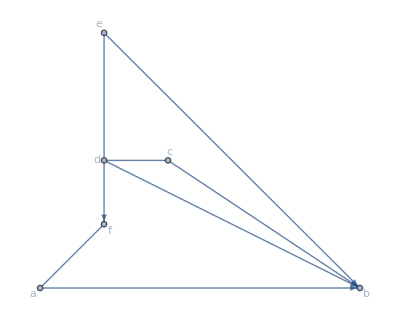

```mathematica
Graph[{a->b,b<->c,c<->d,d->b,d<->e,d->f,f<->a,e->b},VertexLabels->Automatic,GraphLayout->"PlanarEmbedding"]
```

```mathematica
MixedEulerianGraphQ[Graph[{a->b,b<->c,c<->d,d->b,d<->e,d->f,f<->a,e->b},VertexLabels->Automatic,GraphLayout->"PlanarEmbedding"]]
```

False

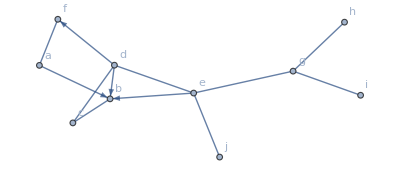

```mathematica
Graph[{a,b,c,d,e,f,g,h,i,j},{a->b,b<->c,c<->d,d->b,d<->e,d->f,f<->a,e->b,g<->e,h<->g,i<->g,j<->e},VertexLabels->Automatic]
```

```mathematica
ConnectedGraphQ[Graph[{a,b,c,d,e,f,g,h,i,j},{a->b,b<->c,c<->d,d->b,d<->e,d->f,f<->a,e->b,g<->e,h<->g,i<->g,j<->e},VertexLabels->Automatic]]
```

True

```mathematica
MixedEulerianGraphQ[Graph[{a,b,c,d,e,f,g,h,i,j},{a->b,b<->c,c<->d,d->b,d<->e,d->f,f<->a,e->b,g<->e,h<->g,i<->g,j<->e},VertexLabels->Automatic]]
```

False

### Timing

```mathematica
MixedEulerianGraphQ[Graph[{a->b,b<->c,c<->d,d->b,d<->e,d->f,f<->a,e->b},VertexLabels->Automatic,GraphLayout->"PlanarEmbedding"]]//RepeatedTiming
```

{0.000641009,False}

```mathematica
MixedEulerianGraphQ[Graph[{a,b,c,d,e,f,g,h,i,j},{a->b,b<->c,c<->d,d->b,d<->e,d->f,f<->a,e->b,g<->e,h<->g,i<->g,j<->e},VertexLabels->Automatic]]//RepeatedTiming
```

{0.0336941,False}

```mathematica
MixedEulerianGraphQ[Graph[{a,b,c,d,e,f,g,h,i,j,k,l,m,n},{a->b,b<->c,c<->d,d->b,d<->e,d->f,f<->a,e->b,g<->e,h<->g,i<->g,j<->e,k<->j,l<->k,m<->l,n<->m},VertexLabels->Automatic]]//RepeatedTiming
```

{0.578724,False}

```mathematica
VertexCount[Graph[{a,b,c,d,e,f,g,h,i,j,k,l,m,n},{a->b,b<->c,c<->d,d->b,d<->e,d->f,f<->a,e->b,g<->e,h<->g,i<->g,j<->e,k<->j,l<->k,m<->l,n<->m},VertexLabels->Automatic]]
```

14

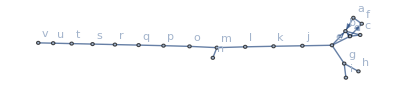

```mathematica
Graph[{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v},{a->b,b<->c,c<->d,d->b,d<->e,d->f,f<->a,e->b,g<->e,h<->g,i<->g,j<->e,k<->j,l<->k,m<->l,n<->m,m<->o,o<->p,p<->q,q<->r,r<->s,s<->t,t<->u,u<->v},VertexLabels->Automatic]
```

```mathematica
MixedEulerianGraphQ[Graph[{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v},{a->b,b<->c,c<->d,d->b,d<->e,d->f,f<->a,e->b,g<->e,h<->g,i<->g,j<->e,k<->j,l<->k,m<->l,n<->m,m<->o,o<->p,p<->q,q<->r,r<->s,s<->t,t<->u,u<->v},VertexLabels->Automatic]]//AbsoluteTiming
```

{218.966,False}

```mathematica
VertexCount[Graph[{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v},{a->b,b<->c,c<->d,d->b,d<->e,d->f,f<->a,e->b,g<->e,h<->g,i<->g,j<->e,k<->j,l<->k,m<->l,n<->m,m<->o,o<->p,p<->q,q<->r,r<->s,s<->t,t<->u,u<->v},VertexLabels->Automatic]]
```

22

### Scope

Text about additional examples expanding scope (and see other sections for options, applications, etc):

```mathematica
MyFunction[x,y,z]
```

x y z

### Options

### Applications

### Properties and Relations

### Possible Issues

The function only works for graphs with a few number of vertexes/nodes.

### Neat Examples

## Source & Additional Information

### Contributed By

Peter Cullen Burbery

### Keywords

keyword 1

### Categories

Cloud & Deployment
 Data Manipulation & Analysis
 External Interfaces & Connections
 Geographic Data & Computation
 Graphs & Networks
 Images
 Knowledge Representation & Natural Language
 Notebook Documents & Presentation
 Repository Tools
 Social, Cultural & Linguistic Data
 Strings & Text
 System Operation & Setup
 User Interface Construction
 Wolfram Physics Project |  Core Language & Structure
 Engineering Data & Computation
 Financial Data & Computation
 Geometry
 Higher Mathematical Computation
 Just For Fun
 Machine Learning
 Programming Utilities
 Scientific and Medical Data & Computation
 Sound & Video
 Symbolic & Numeric Computation
 Time-Related Computation
 Visualization & Graphics

### Related Symbols

SymbolName (documented Wolfram Language symbol)

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Source/Reference Citation

Source, reference or citation information

### Links

Link to other related material

### Tests

```mathematica
MyFunction[x,y]
```

x y

### Compatibility

#### Wolfram Language Version

13.0+

#### Operating System

Windows |  Mac |  Unix

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

## Author Notes

Additional information about limitations, issues, etc.

## Submission Notes

Additional information for the reviewer.